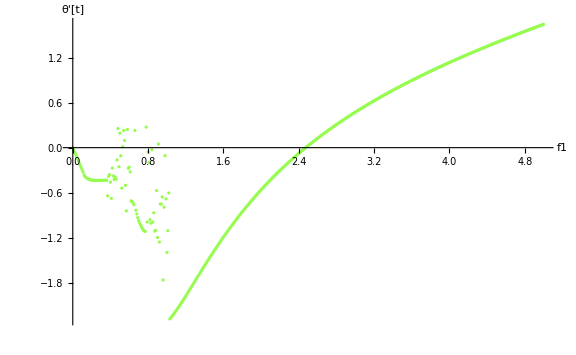

```mathematica
time=200;data={};
v=1.4;a=0.3;b=1;r=0.3;k=1;f=1;(*默认值*)T=2Pi/v;
option=Input[];
Switch[option,v1,v=option,
a1,a=option,
b1,b=option,
r1,r=option,
k1,k=option,
f1,f=option];(*选择要考虑的参数*)
color=RandomReal[{0.1,1},3];
equ={θ''[t]+r θ'[t]-k θ[t]+θ[t]^3==f Cos[v t],θ[0]==a,θ'[0]==b} ;(*当参数变化时，方程组要相应变化*)

Do[s=NDSolve[equ/.option->option1,θ,{t,0,time,T},MaxSteps->Infinity];
AppendTo[data,{option1,(θ/.s[[1]])'[time]}],{option1,0,5,0.01}];
ListPlot[data,PlotStyle->{PointSize[0.004],RGBColor[color]},AxesLabel->{option,"θ'[t]"},ImageSize->Large]
Clear["Global`*"]
```

$Aborted

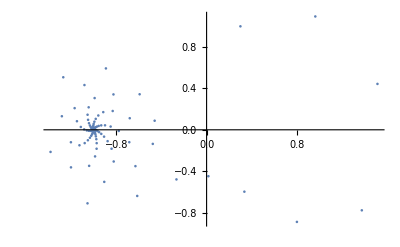

```mathematica
time=2000;data={};

v=10;a=0.3;b=1;r=0.15;k=1;f=0.3;(*默认值*)T=2Pi/v;
(*equ={θ''[t]+0.15 θ'[t]-θ[t]+θ[t]^3==0.3Cos[t],θ[0]==a,θ'[0]==0} ;*)


Do[AppendTo[data,{Evaluate[θ[t2]/.First[NDSolve[{θ''[t]+r θ'[t]-k θ[t]+θ[t]^3==f Cos[v t],θ[0]==a,θ'[0]==b},θ,{t,0,time}]]],Evaluate[θ'[t2]/.First[NDSolve[{θ''[t]+r θ'[t]-k θ[t]+θ[t]^3==f Cos[v t],θ[0]==a,θ'[0]==b},θ,{t,0,time}]]]}],{t2,0,time,T}];
ListPlot[data,PlotRange->All]
Clear["Gloabl`*"]
Clear[Derivative]
```

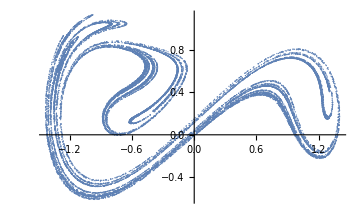

```mathematica
v=1;a=0;b=0;r=0.15;k=1;f=0.3;
data =Module[{},Reap[NDSolve[{θ''[t]+r θ'[t]-k θ[t]+θ[t]^3==f Cos[v t],θ[0]==a,θ'[0]==b,WhenEvent[Mod[t,2π v]==0,Sow[{θ[t],θ'[t]}]]},{},{t,0,100000},MaxSteps->∞]]][[-1,1]];
ListPlot[data,ImageSize->Medium,PlotRange->All,PlotStyle->PointSize[0.0025]]
```

```mathematica
(*这是一个画杜芬振子分岔图的程序*)
v=1.34;r=1;f=1;k=1;  (*默认参数值*)
option=Input[];
Switch[option,
r1,r=option,
k1,k=option,
f1,f=option];(*选择要考虑的参数*)
T=2Pi/v;
m[{a_,b_}]:=Flatten[Reap[NDSolve[{θ''[t]+r θ'[t]-k θ[t]+θ[t]^3==f Cos[v t]/.option->option1,θ[0]==a,θ'[0]==b,WhenEvent[Mod[t,T]==0,Sow[{θ[t],θ'[t]}]]},{},{t,0,T},MaxSteps->Infinity]][[-1,1]],1];(*提取出所需要的点*)

g[{x_,y_}]:={option1,x};
p[{x_,y_}]:={option1,y};(*让横坐标为参数，以考虑参数不同时的情况*)

g1=ListPlot[Flatten[Table[g/@Drop[NestList[m,{1.,0.},100],50],{option1,1,5,0.01}],1],AxesLabel->{option,"θ"},PlotLabel->"位置",LabelStyle->Directive[Bold,Black]]
(*纵坐标是位置*)
g2=ListPlot[Flatten[Table[p/@Drop[NestList[m,{1.,0.},100],50],{option1,1,5,0.01}],1],AxesLabel->{option,"θ'"},PlotLabel->"动量",LabelStyle->Directive[Bold,Black]]

(*纵坐标是速度，质量为1时是动量*)

g3=ListPlot[Flatten[Table[Drop[NestList[m,{1.,0.},100],50],{option1,1,5,0.01}],1],AxesLabel->{"θ","θ'"},PlotLabel->"庞加莱截面",LabelStyle->Directive[Bold,Black]]
(*庞加莱截面*)

Clear["Global`*"]
```

Part::partw: {} 的部分 1 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

$Aborted

$Aborted

Part::partw: {} 的部分 1 不存在.

$Aborted